Manipulating strings

```mathematica
"Ask not for whom the bell tolls" //Head
```

String

```mathematica
earth=AstronomicalData["Earth","Image"]
```

-Graphics-

```mathematica
GenomeData["SNORD107"]
```

GGTTCATGATGACACAGGACCTTGTCTGAACATAATGATTTCAAAATTTGAGCTTAAAAATGACACTCTGAAATC

```mathematica
StringQ[%]
```

True

```mathematica
CharacterRange[" ","~"]
```

{ ,!,",#,$,%,&,',(,),*,+,,,-,.,/,0,1,2,3,4,5,6,7,8,9,:,;,<,=,>,?,@,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,{,|,},~}

```mathematica
CharacterRange["α","ω"]
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,ς,σ,τ,υ,φ,χ,ψ,ω}

```mathematica
ToCharacterCode[{"天","高","皇","帝","远"}]
```

{{22825},{39640},{30343},{24093},{36828}}

```mathematica
FromCharacterCode[{22825,39640,30343,24093,36828}]
```

天高皇帝远

```mathematica
Sort[{"a","b","d","x","c","d"}]
```

{a,b,c,d,d,x}

```mathematica
Sort[{"天","高","皇","帝","远"}]
```

{天,帝,皇,远,高}

```mathematica
StringTake["Ask not for whom the bell tolls",10]
```

Ask not fo

```mathematica
StringJoin["天","高","皇","帝","远"]
```

天高皇帝远

```mathematica
"x"<>"2"
```

x2

```mathematica
Head[%]
```

String

```mathematica
%%===x2
```

False

```mathematica
StringTrim["http://www.google.com/","http://" | "/"]
```

www.google.com

```mathematica
StringReverse["abcde"]
```

edcba

```mathematica
StringDrop["abcde",-1]
```

abcd

```mathematica
StringPosition["abcdefgbc","bc"]
```

{{2,3},{8,9}}

```mathematica
StringInsert["abcde","X",3]
```

abXcde

```mathematica
StringReplace["21/02/2018","/"->"-"]
```

21-02-2018

```mathematica
ToExpression["x"<>"2"]
```

x2

```mathematica
Head[%]
```

Symbol

```mathematica
ToExpression["x"<>ToString[#]&/@Range[6]]
```

{x1,x2,x3,x4,x5,x6}

```mathematica
makevarlist[x_Symbol,n_Integer]:=
ToExpression[
ToString[x]<>ToString[#]&/@Range[n]]
```

```mathematica
makevarlist[tmp,10]
```

{tmp1,tmp2,tmp3,tmp4,tmp5,tmp6,tmp7,tmp8,tmp9,tmp10}

```mathematica
%⟦1⟧//Head
```

Symbol

```mathematica
chars = Characters["tame"]
```

{t,a,m,e}

```mathematica
perms=Permutations[chars]
```

{{t,a,m,e},{t,a,e,m},{t,m,a,e},{t,m,e,a},{t,e,a,m},{t,e,m,a},{a,t,m,e},{a,t,e,m},{a,m,t,e},{a,m,e,t},{a,e,t,m},{a,e,m,t},{m,t,a,e},{m,t,e,a},{m,a,t,e},{m,a,e,t},{m,e,t,a},{m,e,a,t},{e,t,a,m},{e,t,m,a},{e,a,t,m},{e,a,m,t},{e,m,t,a},{e,m,a,t}}

```mathematica
words=StringJoin/@perms
```

{tame,taem,tmae,tmea,team,tema,atme,atem,amte,amet,aetm,aemt,mtae,mtea,mate,maet,meta,meat,etam,etma,eatm,eamt,emta,emat}

```mathematica
Select[words,DictionaryLookup[#,IgnoreCase->True]≠ {}&]
```

{tame,team,mate,meta,meat}

```mathematica
anagrams[word_String]:=
Module[{chars,words},
chars= Characters[word];
words= StringJoin/@Permutations[chars];
Select[words,DictionaryLookup[#,IgnoreCase->True]≠ {}&]
             ]
```

```mathematica
anagrams["instance"]//Timing
```

{0.778315,{instance,ancients,canniest}}

A first look at graphics

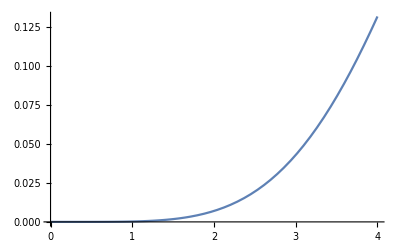

```mathematica
Plot[BesselJ[5,x],{x,0,4}]
```

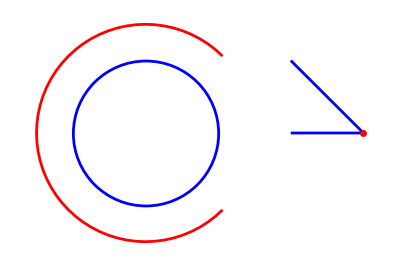

```mathematica
Graphics[{
Blue,AbsoluteThickness[2],Line[{{0,0},{1,0},{0,1}}],
Red,AbsolutePointSize[5],Point[{1,0}],
Blue,Circle[{-2,0},1],Red,Circle[{-2,0},1.5,{π/4,7π/4}]}
                   ]
```

```mathematica
?Circle
```

```mathematica
?EdgeForm
```

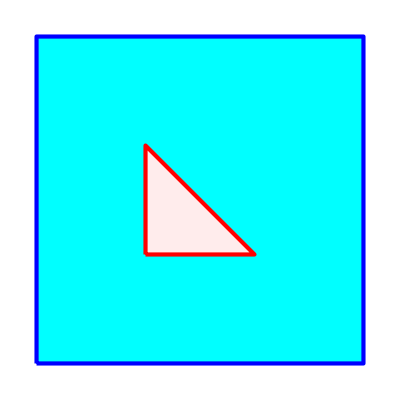

```mathematica
Graphics[{
{Cyan,EdgeForm[{AbsoluteThickness[3],RGBColor[0,0,1]}],Rectangle[{-1,-1},{2,2}]},
{EdgeForm[{AbsoluteThickness[3],RGBColor[1,0,0]}],FaceForm[LightPink],Polygon[{{0,0},{1,0},{0,1}}]}
 }
                   ]
```

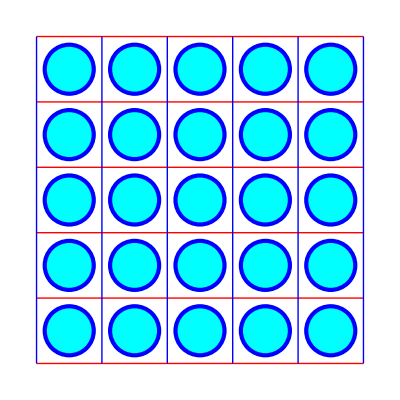

```mathematica
Graphics[{
Red,Table[Line[{{0,y},{1,y}}], {y,0,1,0.2}],
Blue,Table[Line[{{x,0},{x,1}}], {x,0,1,0.2}],
 Cyan, EdgeForm[{AbsoluteThickness[3],RGBColor[0,0,1]}],Table[Disk[{x,y},0.075],{x,0.1,0.9,0.2},{y,0.1,0.9,0.2}]}
                 ]
```

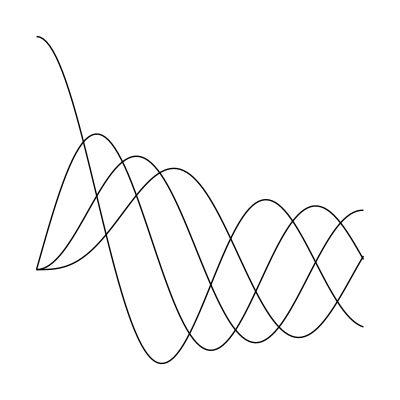

```mathematica
Graphics[{
Line[ Table[{x, BesselJ[n,x]},{n,0,3},{x,0,10,0.1}] ]},
  AspectRatio->1
                  ]
```

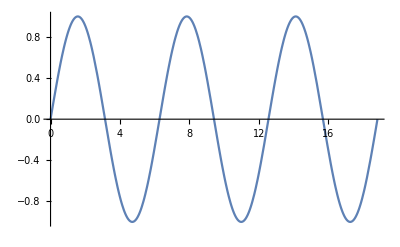

```mathematica
Plot[Sin[x],{x,0,6Pi},
         ImageSize->400]
```

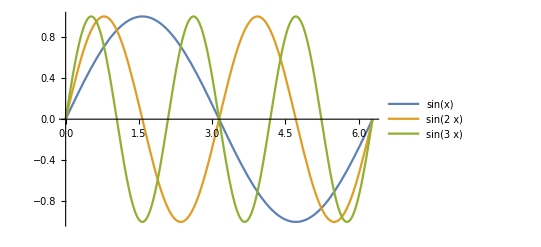

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},
          PlotLegends->"Expressions",
          ImageSize->400]
```

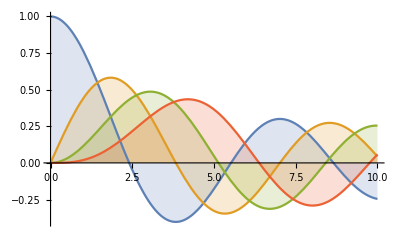

```mathematica
g1=
Plot[Evaluate[Table[BesselJ[n,x],{n,0,3}]],{x,0,10},
         Filling->Axis,
        ImageSize->400]
```

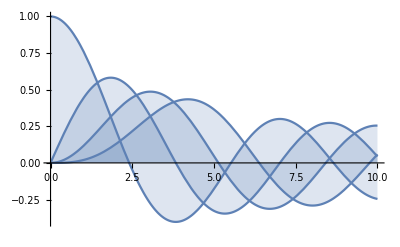

```mathematica
g2=Plot[Table[BesselJ[n,x],{n,0,3}],{x,0,10},
         Filling->Axis,
        ImageSize->400]
```

```mathematica
f[n_,x_]:= Abs[((1/Pi)^(1/4)HermiteH[n,x])/(E^(x^2/2)Sqrt[2^n n!])]^2
```

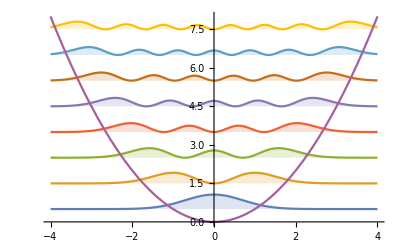

```mathematica
Plot[Evaluate@
  Append[Table[f[n,x]+n+1/2,{n,0,7}],x^2/2],{x,-4,4},Filling-> Table[n->n-1/2,{n,1,8}],
ImageSize->400]
```

```mathematica
Clear[f]
```

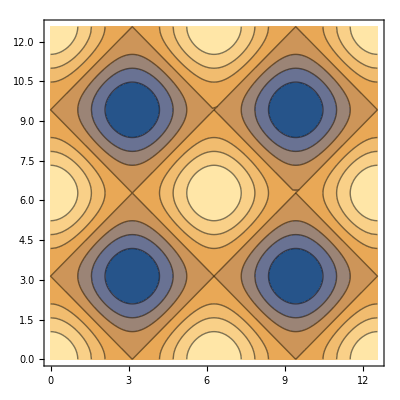

```mathematica
g3=ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},
                         ImageSize->400]
```

```mathematica
Options[ContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

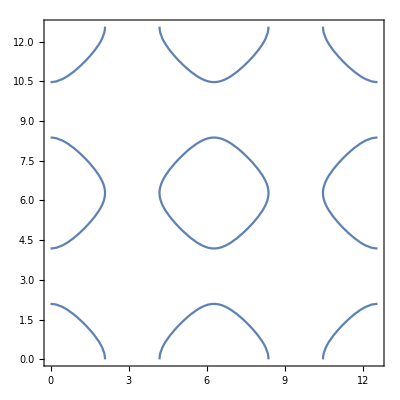

```mathematica
g4=ContourPlot[Cos[x]+Cos[y]==1/2,{x,0,4Pi},{y,0,4Pi}]
```

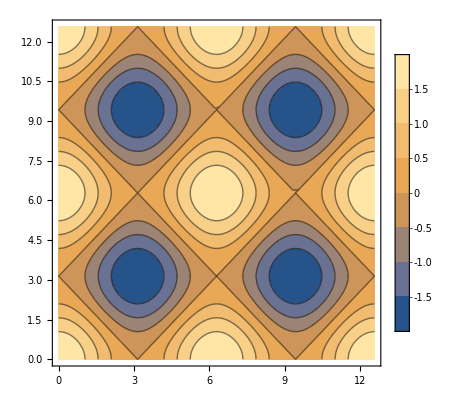

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},PlotLegends->Automatic]
```

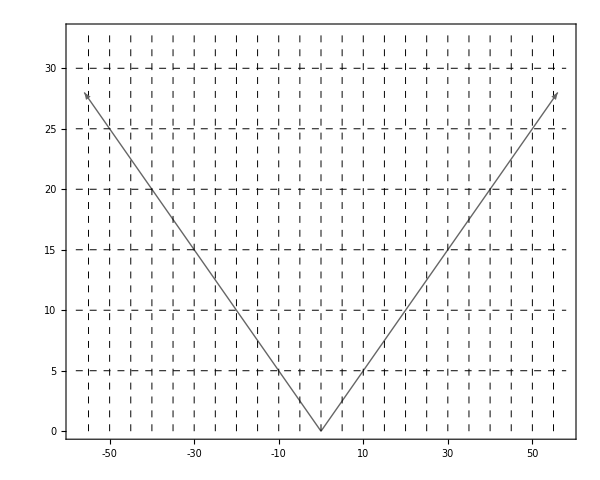

```mathematica
Graphics[{AbsoluteThickness[1],GrayLevel[0.4],Arrowheads[0.03],
Arrow[{{0,0},{56,28}}],Arrow[{{0,0},{-56,28}}],
{Dashed,Black,AbsoluteThickness[0.7],
Table[Line[{{k,0},{k,33}}],{k,-55,55,5}],
Table[Line[{{-58,k},{58,k}}],{k,5,30,5}]},
GrayLevel[0.2]},
AspectRatio->0.8,
PlotRange->{{-58,58},{0,33}},
Frame->True,
FrameTicks->{{Table[Which[Mod[n,10]==0,{n,n,{0.02,0}},
                                                 Mod[n,5]==0,{n,n,{0.015,0}},
                                                True,{n,Null,{0.01,0}}],{n,0,33}],
                         Table[Which[Mod[n,10]==0,{n,Null,{0.02,0}},
                                               Mod[n,5]==0,{n,Null,{0.015,0}},
                                               True,{n,Null,{0.01,0}}],{n,0,33}]},
                         {Table[Which[Mod[n,10]==0,{n,If[n≥0,n ,n Spacer[10]],{0.02,0}},
                                                Mod[n,5]==0,{n,Null,{0.015,0}},
                                               True,{n,Null,{0.01,0}}],{n,-58,58}],
                          Table[Which[Mod[n,10]==0,{n,Null,{0.02,0}},
                                                Mod[n,5]==0,{n,Null,{0.015,0}},
                                                True,{n,Null,{0.01,0}}],{n,-58,58}]} },
FrameStyle->Directive[{FontFamily->"Times", FontSize->17}],
ImageSize->600]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},
             ColorFunction->"Rainbow",
              ImageSize->400,
               BoxRatios->{1,1,1}
                ](*You can actually use a different function for the colour*)
```

-Graphics3D-

```mathematica
?ViewPoint
```

```mathematica
?Opacity
```

Opacity!

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},
             PlotStyle-> Opacity[0.5] ]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(3+Cos[v])Cos[u],(3+Cos[v])Sin[u],Sin[v]},{u,0,2Pi},{v,0,2Pi},
   ImageSize->400,
       Ticks->False]
```

-Graphics3D-

```mathematica
?ColorData
```

```mathematica
?ColorFunction
```

```mathematica
g1
```

-Graphics-

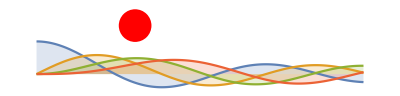

```mathematica
Show[{g1,
Graphics[{Red,Disk[{3,1.5},0.5]}]},
Axes->False,
PlotRange->All,
AspectRatio->Automatic]
```

```mathematica
?GraphicsGrid
```

GraphicsGrid[{{g_11,g_12,…},…}] generates a graphic in which the g_ij are laid out in a two-dimensional grid.

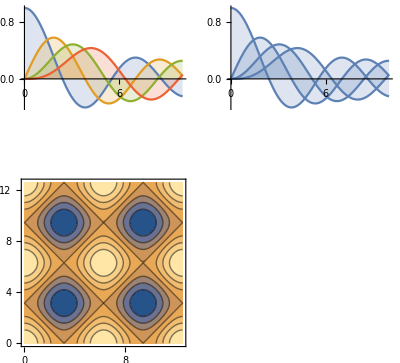

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}},
ImageSize->400]
```

A second look at graphics

### A graphic illustrating analytic continuation

```mathematica
ψ[n_]:=-(3/2)^n 1/50
```

```mathematica
Table[N[ψ[n]],{n,0,4}]
```

{-0.02,-0.03,-0.045,-0.0675,-0.10125}

```mathematica
N[-1/7]
```

-0.142857

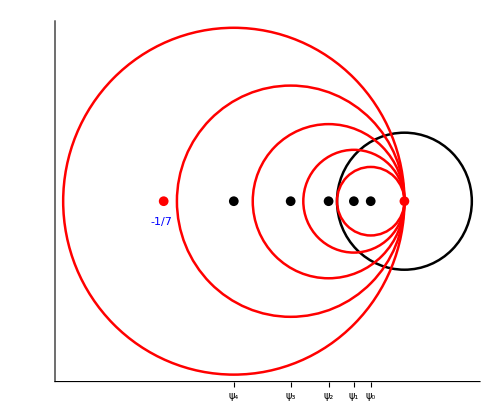

```mathematica
Graphics[{
AbsoluteThickness[1.8], 
Black,Circle[{0,0},1/25],
Red,Table[Circle[{ψ[n],0},Abs[ψ[n]]],{n,0,4}],
AbsolutePointSize[7],Black,Point[Table[{ψ[n],0},{n,0,4}]],
Red,Point[{-1/7,0}],Point[{0,0}],
Blue,Text[-1/7,{-1/7-0.0015,-0.012}]},(*position for the -1/7*)
ImageSize->500,
Axes->True,
AxesStyle->Directive[GrayLevel[0.6],12],
Method->{"AxesInFront"->False},(*If not, it puts the axes over the dots!*)
Ticks->{Table[{ψ[n],Subscript[ψ, n]},{n,0,4}],None},
TicksStyle-> Directive[Blue,FontFamily->"Computer Modern",FontSize->15]
                ]
```

```mathematica
1/(14ψ[4])//N
```

-0.705467

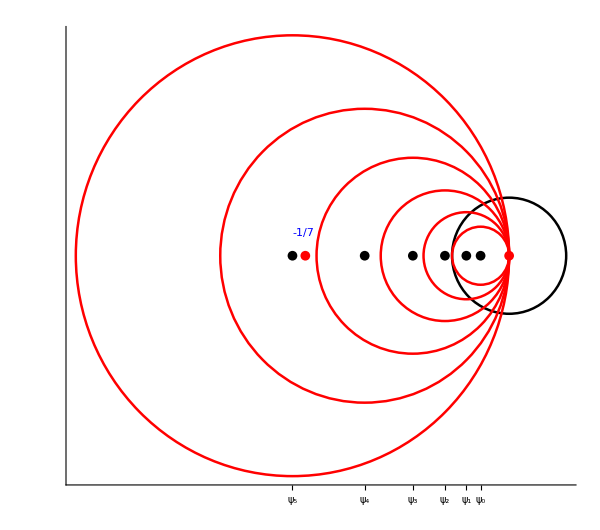

```mathematica
Graphics[{
AbsoluteThickness[1.8], (* GrayLevel[0.6],Line[{{-0.215,0},{0.05,0}}],Line[{{0,-0.11},{0,0.11}}], *)
Black,Circle[{0,0},1/25],
Red,Table[Circle[{ψ[n],0},Abs[ψ[n]]],{n,0,5}],
AbsolutePointSize[7],Black,Point[Table[{ψ[n],0},{n,0,5}]],
Red,Point[{-1/7,0}],Point[{0,0}],
Blue,Text[-1/7,{-1/7-0.0015,0.016}]},
ImageSize->600,
Axes->True,
AxesStyle->Directive[GrayLevel[0.6],12],
Method->{"AxesInFront"->False},
Ticks->{Table[{ψ[n],Subscript[ψ, n]},{n,0,5}],None},
TicksStyle-> Directive[Blue,FontFamily->"Computer Modern",FontSize->17]
                ]
```

### A hypocycloid

```mathematica
center[r_,θ_]:=(1-r){Sin[θ],-Cos[θ]}

pt[r_,θ_]:= center[r,θ]-r {Sin[(1-r)/r θ], Cos[(1-r)/r θ]}
```

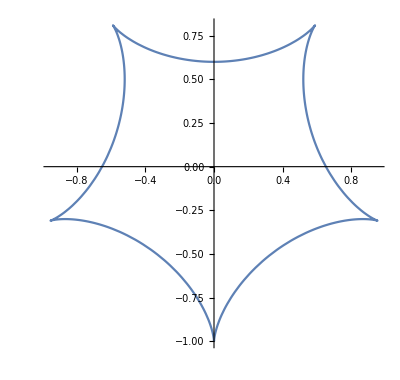

```mathematica
ParametricPlot[pt[1/5,θ],{θ,0,2π}]
```

```mathematica
hcyc[r_,ϕ_]:=
Show[
ParametricPlot[pt[r,θ],{θ,0,ϕ}],
Graphics[{AbsoluteThickness[3],Circle[{0,0},1], Circle[center[r,ϕ],r], Line[{center[r,ϕ],pt[r,ϕ]}],
AbsolutePointSize[6.5],Point[center[r,ϕ]], Red, Point[pt[r,ϕ]]}],
PlotRange->{{-1.1,1.1},{-1.1,1.1}},
Frame->True,
ImageSize->600
        ]
```

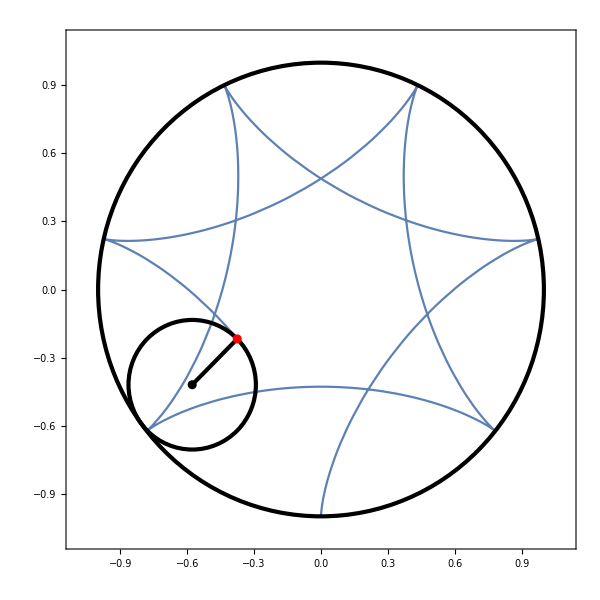

```mathematica
hcyc[2/7,3.7π]
```

```mathematica
Animate[hcyc[2/9,ϕ],{ϕ,0,4π}]
```

### Zeta function data for the manifold AESZ34

```mathematica
SetDirectory["/Users/old philip/Dropbox/DucoPhilipXenia/Mathfiles/Top Copies"];

AESZ34list=<<mfldAESZ34data.nb;
```

```mathematica
KirasPlot=
Show[  
Graphics[{AbsoluteThickness[2],GrayLevel[0.7],Line[{{-4,-2},{4,-2},{4,6},{-4,6},{-4,-2}}],Arrow[{{-4,0},{5,0}}],Arrow[{{0,-2},{0,7}}]} ],
          Plot[{x^2/4+2,2Abs[x]-2},{x,-4,4},
        Filling->{1->{2}},
        PlotStyle->Directive[Black,AbsoluteThickness[2]]],
           Axes-> False,
           PlotRange->{{-5.1,5.1},{-2.1,7.1}},
           AspectRatio->Automatic,
           ImageSize->600
        ];
 

figAESZ34[p_]:=
Show[KirasPlot,
         Graphics[{AbsolutePointSize[2.0],Red,
                          Point[N[{(#⟦1⟧)/p^(3/2),(#⟦2⟧)/p^2}]&/@(Last/@(Select[Select[AESZ34list,#⟦1⟧==p&]⟦1,2⟧,#⟦2⟧=="smooth"&]))]}] ]
```

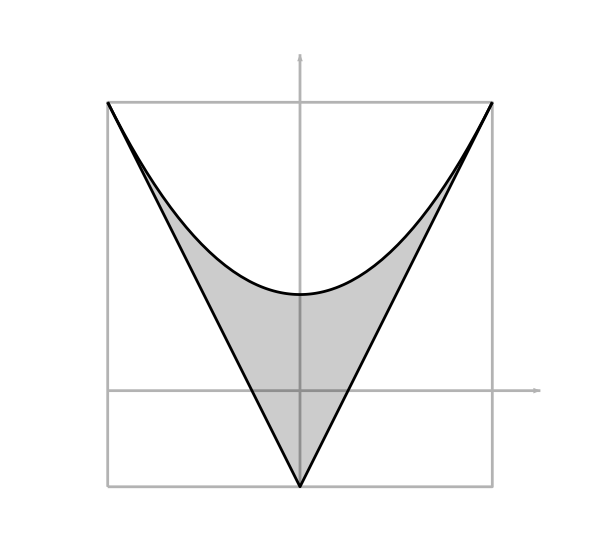

```mathematica
KirasPlot
```

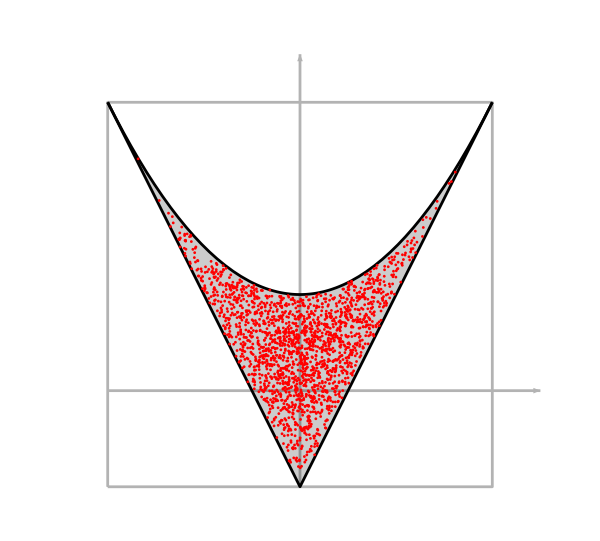

```mathematica
figAESZ34[2003]
```

```mathematica
Manipulate[
figAESZ34[Prime[j]],
{{j,137,"n'th prime"},3,502,1,Appearance->"Labeled"}]
```

```mathematica
cumulativeplot=
Show[KirasPlot,
         Graphics[{AbsolutePointSize[0.2],Red,
                           Point[
                             Flatten[
                                Table[p=Prime[j]; 
                                       N[{(#⟦1⟧)/p^(3/2),(#⟦2⟧)/p^2}]&/@(Last/@Select[AESZ34list⟦j-2,2⟧,#⟦2⟧=="smooth"&]),{j,3,502}],1]]}]
        ]
```

-Graphics-

Parallelisation

Which Mersenne numbers are primes?

```mathematica
Module[{p,q},
Table[p=Prime[j];q=2^p-1;{p,q,PrimeQ[q]},{j,1,20}]
              ]//Column
```

{2,3,True}
{3,7,True}
{5,31,True}
{7,127,True}
{11,2047,False}
{13,8191,True}
{17,131071,True}
{19,524287,True}
{23,8388607,False}
{29,536870911,False}
{31,2147483647,True}
{37,137438953471,False}
{41,2199023255551,False}
{43,8796093022207,False}
{47,140737488355327,False}
{53,9007199254740991,False}
{59,576460752303423487,False}
{61,2305843009213693951,True}
{67,147573952589676412927,False}
{71,2361183241434822606847,False}

```mathematica
2^11-1
```

2047

```mathematica
FactorInteger[%]
```

{{23,1},{89,1}}

```mathematica
mprimes[n_]:=
Module[{p},
Select[
Table[p=Prime[j];{p,2^p-1},{j,1,n}],PrimeQ[#⟦2⟧]&] (*2nd elements of table[] being the number of interest*)
              ]
```

```mathematica
{tim,mp1000}=AbsoluteTiming[mprimes[1000]];
```

```mathematica
tim
```

33.6147

```mathematica
mp1000//Column
```

{2,3}
{3,7}
{5,31}
{7,127}
{13,8191}
{17,131071}
{19,524287}
{31,2147483647}
{61,2305843009213693951}
{89,618970019642690137449562111}
{107,162259276829213363391578010288127}
{127,170141183460469231731687303715884105727}
{521,6864797660130609714981900799081393217269435300143305409394463459185543183397656052122559640661454554977296311391480858037121987999716643812574028291115057151}
{607,531137992816767098689588206552468627329593117727031923199444138200403559860852242739162502265229285668889329486246501015346579337652707239409519978766587351943831270835393219031728127}
{1279,10407932194664399081925240327364085538615262247266704805319112350403608059673360298012239441732324184842421613954281007791383566248323464908139906605677320762924129509389220345773183349661583550472959420547689811211693677147548478866962501384438260291732348885311160828538416585028255604666224831890918801847068222203140521026698435488732958028878050869736186900714720710555703168729087}
{2203,1475979915214180235084898622737381736312066145333169775147771216478570297878078949377407337049389289382748507531496480477281264838760259191814463365330269540496961201113430156902396093989090226259326935025281409614983499388222831448598601834318536230923772641390209490231836446899608210795482963763094236630945410832793769905399982457186322944729636418890623372171723742105636440368218459649632948538696905872650486914434637457507280441823676813517852099348660847172579408422316678097670224011990280170474894487426924742108823536808485072502240519452587542875349976558572670229633962575212637477897785501552646522609988869914013540483809865681250419497686697771007}
{2281,446087557183758429571151706402101809886208632412859901111991219963404685792820473369112545269003989026153245931124316702395758705693679364790903497461147071065254193353938124978226307947312410798874869040070279328428810311754844108094878252494866760969586998128982645877596028979171536962503068429617331702184750324583009171832104916050157628886606372145501702225925125224076829605427173573964812995250569412480720738476855293681666712844831190877620606786663862190240118570736831901886479225810414714078935386562497968178729127629594924411960961386713946279899275006954917139758796061223803393537381034666494402951052059047968693255388647930440925104186817009640171764133172418132836351}
{3217,259117086013202627776246767922441530941818887553125427303974923161874019266586362086201209516800483406550695241733194177441689509238807017410377709597512042313066624082916353517952311186154862265604547691127595848775610568757931191017711408826252153849035830401185072116424747461823031471398340229288074545677907941037288235820705892351068433882986888616658650280927692080339605869308790500409503709875902119018371991620994002568935113136548829739112656797303241986517250116412703509705427773477972349821676443446668383119322540099648994051790241624056519054483690809616061625743042361721863339415852426431208737266591962061753535748892894599629195183082621860853400937932839420261866586142503251450773096274235376822938649407127700846077124211823080804139298087057504713825264571448379371125032081826126566649084251699453951887789613650248405739378594599444335231188280123660406262468609212150349937584782292237144339628858485938215738821232393687046160677362909315071}
{4253,190797007524439073807468042969529173669356994749940177394741882673528979787005053706368049835514900244303495954950709725762186311224148828811920216904542206960744666169364221195289538436845390250168663932838805192055137154390912666527533007309292687539092257043362517857366624699975402375462954490293259233303137330643531556539739921926201438606439020075174723029056838272505051571967594608350063404495977660656269020823960825567012344189908927956646011998057988548630107637380993519826582389781888135705408653045219655801758081251164080554609057468028203308718724654081055323215860189611391296030471108443146745671967766308925858547271507311563765171008318248647110097614890313562856541784154881743146033909602737947385055355960331855614540900081456378659068370317267696980001187750995491090350108417050917991562167972281070161305972518044872048331306383715094854938415738549894606070722584737978176686422134354526989443028353644037187375385397838259511833166416134323695660367676897722287918773420968982326089026150031515424165462111337527431154890666327374921446276833564519776797633875503548665093914556482031482248883127023777039667707976559857333357013727342079099064400455741830654320379350833236245819348824064783585692924881021978332974949906122664421376034687815350484991}
{4423,285542542228279613901563566102164008326164238644702889199247456602284400390600653875954571505539843239754513915896150297878399377056071435169747221107988791198200988477531339214282772016059009904586686254989084815735422480409022344297588352526004383890632616124076317387416881148592486188361873904175783145696016919574390765598280188599035578448591077683677175520434074287726578006266759615970759521327828555662781678385691581844436444812511562428136742490459363212810180276096088111401003377570363545725120924073646921576797146199387619296560302680261790118132925012323046444438622308877924609373773012481681672424493674474488537770155783006880852648161513067144814790288366664062257274665275787127374649231096375001170901890786263324619578795731425693805073056119677580338084333381987500902968831935913095269821311141322393356490178488728982288156282600813831296143663845945431144043753821542871277745606447858564159213328443580206422714694913091762716447041689678070096773590429808909616750452927258000843500344831628297089902728649981994387647234574276263729694848304750917174186181130688518792748622612293341368928056634384466646326572476167275660839105650528975713899320211121495795311427946254553305387067821067601768750977866100460014602138408448021225053689054793742003095722096732954750721718115531871310231057902608580607}

```mathematica
Length[mp1000]
```

20

```mathematica
parallelmprimes[n_]:=
Module[{p,q},
ParallelTable[p=Prime[j];q=2^p-1;If[PrimeQ[q],{p,q},Nothing],{j,1,n},Method->"FinestGrained"]
             ]
```

Since we perform each check individually, we can ‘parallize’ this - i.e. do more at the same time. The method is here to make this more efficient - rather than waiting for all parallel computations to finish, we can assign a new calculation to the kernels that already finished.

```mathematica
?ParallelTable
```

```mathematica
{tim,parallelmp1000}=AbsoluteTiming[parallelmprimes[1000]];
```

```mathematica
tim
```

21.6988

```mathematica
parallelmp1000//Column
```

{2,3}
{3,7}
{5,31}
{7,127}
{13,8191}
{17,131071}
{19,524287}
{31,2147483647}
{61,2305843009213693951}
{89,618970019642690137449562111}
{107,162259276829213363391578010288127}
{127,170141183460469231731687303715884105727}
{521,6864797660130609714981900799081393217269435300143305409394463459185543183397656052122559640661454554977296311391480858037121987999716643812574028291115057151}
{607,531137992816767098689588206552468627329593117727031923199444138200403559860852242739162502265229285668889329486246501015346579337652707239409519978766587351943831270835393219031728127}
{1279,10407932194664399081925240327364085538615262247266704805319112350403608059673360298012239441732324184842421613954281007791383566248323464908139906605677320762924129509389220345773183349661583550472959420547689811211693677147548478866962501384438260291732348885311160828538416585028255604666224831890918801847068222203140521026698435488732958028878050869736186900714720710555703168729087}
{2203,1475979915214180235084898622737381736312066145333169775147771216478570297878078949377407337049389289382748507531496480477281264838760259191814463365330269540496961201113430156902396093989090226259326935025281409614983499388222831448598601834318536230923772641390209490231836446899608210795482963763094236630945410832793769905399982457186322944729636418890623372171723742105636440368218459649632948538696905872650486914434637457507280441823676813517852099348660847172579408422316678097670224011990280170474894487426924742108823536808485072502240519452587542875349976558572670229633962575212637477897785501552646522609988869914013540483809865681250419497686697771007}
{2281,446087557183758429571151706402101809886208632412859901111991219963404685792820473369112545269003989026153245931124316702395758705693679364790903497461147071065254193353938124978226307947312410798874869040070279328428810311754844108094878252494866760969586998128982645877596028979171536962503068429617331702184750324583009171832104916050157628886606372145501702225925125224076829605427173573964812995250569412480720738476855293681666712844831190877620606786663862190240118570736831901886479225810414714078935386562497968178729127629594924411960961386713946279899275006954917139758796061223803393537381034666494402951052059047968693255388647930440925104186817009640171764133172418132836351}
{3217,259117086013202627776246767922441530941818887553125427303974923161874019266586362086201209516800483406550695241733194177441689509238807017410377709597512042313066624082916353517952311186154862265604547691127595848775610568757931191017711408826252153849035830401185072116424747461823031471398340229288074545677907941037288235820705892351068433882986888616658650280927692080339605869308790500409503709875902119018371991620994002568935113136548829739112656797303241986517250116412703509705427773477972349821676443446668383119322540099648994051790241624056519054483690809616061625743042361721863339415852426431208737266591962061753535748892894599629195183082621860853400937932839420261866586142503251450773096274235376822938649407127700846077124211823080804139298087057504713825264571448379371125032081826126566649084251699453951887789613650248405739378594599444335231188280123660406262468609212150349937584782292237144339628858485938215738821232393687046160677362909315071}
{4253,190797007524439073807468042969529173669356994749940177394741882673528979787005053706368049835514900244303495954950709725762186311224148828811920216904542206960744666169364221195289538436845390250168663932838805192055137154390912666527533007309292687539092257043362517857366624699975402375462954490293259233303137330643531556539739921926201438606439020075174723029056838272505051571967594608350063404495977660656269020823960825567012344189908927956646011998057988548630107637380993519826582389781888135705408653045219655801758081251164080554609057468028203308718724654081055323215860189611391296030471108443146745671967766308925858547271507311563765171008318248647110097614890313562856541784154881743146033909602737947385055355960331855614540900081456378659068370317267696980001187750995491090350108417050917991562167972281070161305972518044872048331306383715094854938415738549894606070722584737978176686422134354526989443028353644037187375385397838259511833166416134323695660367676897722287918773420968982326089026150031515424165462111337527431154890666327374921446276833564519776797633875503548665093914556482031482248883127023777039667707976559857333357013727342079099064400455741830654320379350833236245819348824064783585692924881021978332974949906122664421376034687815350484991}
{4423,285542542228279613901563566102164008326164238644702889199247456602284400390600653875954571505539843239754513915896150297878399377056071435169747221107988791198200988477531339214282772016059009904586686254989084815735422480409022344297588352526004383890632616124076317387416881148592486188361873904175783145696016919574390765598280188599035578448591077683677175520434074287726578006266759615970759521327828555662781678385691581844436444812511562428136742490459363212810180276096088111401003377570363545725120924073646921576797146199387619296560302680261790118132925012323046444438622308877924609373773012481681672424493674474488537770155783006880852648161513067144814790288366664062257274665275787127374649231096375001170901890786263324619578795731425693805073056119677580338084333381987500902968831935913095269821311141322393356490178488728982288156282600813831296143663845945431144043753821542871277745606447858564159213328443580206422714694913091762716447041689678070096773590429808909616750452927258000843500344831628297089902728649981994387647234574276263729694848304750917174186181130688518792748622612293341368928056634384466646326572476167275660839105650528975713899320211121495795311427946254553305387067821067601768750977866100460014602138408448021225053689054793742003095722096732954750721718115531871310231057902608580607}

```mathematica
circ[z_]:=
ContourPlot[x^2+y^2-z^2==0,{x,-1,1},{y,-1,1},
PlotRange->All,PlotPoints->100,ContourStyle->Directive[{AbsoluteThickness[1.5],RGBColor[1,0,0]}] ]
```

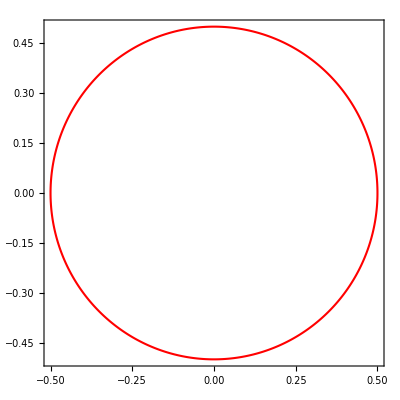

```mathematica
circ[0.5]
```

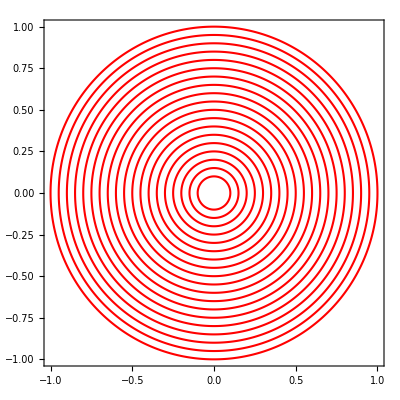

```mathematica
Show[
ParallelTable[circ[z],{z,0.1,1,0.05}]
]
```

### Interesting graphic

```mathematica
G[σ_,τ_]:=(1-σ+σ^2) (1-τ+τ^2) (1-σ τ+σ^2 τ^2)-1/2 σ τ (1+σ) (1+τ) (1+σ τ)+3 σ^2 τ^2

H[σ_,τ_]:=σ τ (1-σ) (1-τ) (1-σ τ)

SubPlus[F][σ_,τ_,ψ_]:=G[σ,τ]+√(32/ψ^5-3/4) H[σ,τ]
SubMinus[F][σ_,τ_,ψ_]:=G[σ,τ]-√(32/ψ^5-3/4) H[σ,τ]

f[s_]:=(2s)/((s+1)(2-s))(*map line to some range*)
```

```mathematica
plusplot[z_]:=ContourPlot[SubPlus[F][σ,τ,z^(1/5)]==0,{σ,-6,7},{τ,-6,7},PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],RGBColor[1,0,0]}]]

minusplot[z_]:=ContourPlot[SubMinus[F][σ,τ,z^(1/5)]==0,{σ,-6,7},{τ,-6,7},PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],RGBColor[0,0,1]}]]

sigmatauplot:=ContourPlot[σ τ - 1==0,{σ,-6,7},{τ,-6,7},PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],GrayLevel[0.6]}]]


noncompactplot[z_]:=
Show[
plusplot[z],minusplot[z],sigmatauplot,
Graphics[{AbsoluteThickness[1.5],GrayLevel[0.6],Line[{{0,-6},{0,7}}],Line[{{1,-6},{1,7}}],Line[{{-6,0},{7,0}}],Line[{{-6,1},{7,1}}]}],
PlotRange->{{-6,7},{-6,7}},
Axes->False,
Frame->False,
ImageSize->300
     ]
```

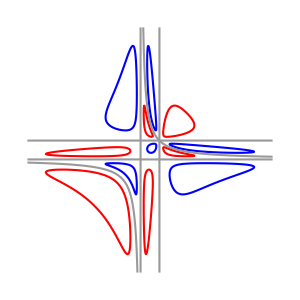

```mathematica
noncompactplot[0.5]
```

Map now everyting to a finite range using the previous f function:

```mathematica
cplusplot[z_]:=
ContourPlot[SubPlus[F][f[s],f[t],z^(1/5)]==0,{s,-1+10^-6,2-10^-6},{t,-1+10^-6,2-10^-6},(*the 10^-6 here just saves some time*)
PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],RGBColor[1,0,0]}]]

cminusplot[z_]:=
ContourPlot[SubMinus[F][f[s],f[t],z^(1/5)]==0,{s,-1+10^-6,2-10^-6},{t,-1+10^-6,2-10^-6},
PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],RGBColor[0,0,1]}]]

csigmatauplot:=
ContourPlot[f[s] f[t] - 1==0,{s,-1+10^-6,2-10^-6},{t,-1+10^-6,2-10^-6},
PlotPoints->100, ContourStyle->Directive[{AbsoluteThickness[1.5],GrayLevel[0.6]}]]

lines=Join[ Table[Line[{{j,-1},{j,2}}],{j,-1,2}], Table[Line[{{-1,k},{2,k}}],{k,-1,2}]];

points=Point[{{1,1},{-1,0},{2,0},{0,-1},{0,2}}];


compactplot[z_]:=
Show[
cplusplot[z],cminusplot[z],csigmatauplot,
Graphics[{AbsoluteThickness[1.5],GrayLevel[0.7],lines, AbsolutePointSize[6],Darker[Red], points}],
PlotRange->{{-1.1,2.1},{-1.1,2.1}},
Axes->False,
Frame->False,
ImageSize->300
           ]
```

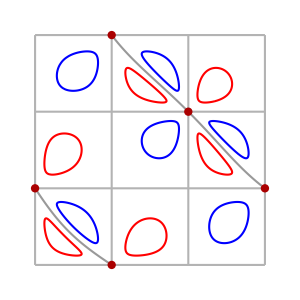
{3.7904,-Graphics-}

```mathematica
AbsoluteTiming[compactplot[0.5]] (*this is actually a torus*)
```

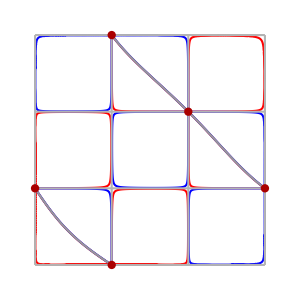
{6.56607,-Graphics-}

```mathematica
AbsoluteTiming[compactplot[10^-4]]
```

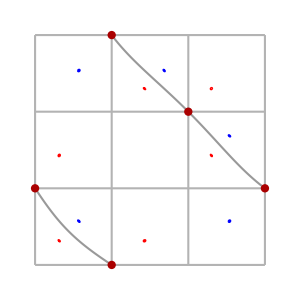
{2.92261,-Graphics-}

```mathematica
AbsoluteTiming[compactplot[0.999]]
```

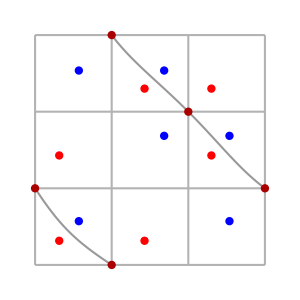

```mathematica
finv[σ_]:=(σ-2+√(9 σ^2-4σ+4))/(2σ)

redsings=
{{1/2 (-1-√5),1/2 (-1-√5)},{1/2 (-1-√5),1/2 (3-√5)},{1/2 (3-√5),1/2 (-1-√5)},{1/2 (3-√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (3-√5)},{1/2 (1+√5),1/2 (1+√5)}};

bluesings= redsings/.{√5->-√5};

conifoldplot=
Show[
csigmatauplot,
Graphics[{AbsoluteThickness[1.5],GrayLevel[0.7],lines, AbsolutePointSize[6],Darker[Red], points,
Red,Point[finv/@redsings],Blue,Point[finv/@bluesings]}],
PlotRange->{{-1.1,2.1},{-1.1,2.1}},
Axes->False,
Frame->False,
ImageSize->300
           ]
```

The following is a table of 51 plots and takes a few minutes. There is no displayed output.

```mathematica
{tim,plottab}=
AbsoluteTiming[
Join[
Table[compactplot[z],{z,0.005,0.995,0.99/50}], {conifoldplot}]
                                ];

tim
```

208.85

```mathematica
Show[plottab]
```

-Graphics-

```mathematica
{tim, parallelplottab}=
AbsoluteTiming[
Append[
ParallelTable[
G[σ_,τ_]:=(1-σ+σ^2) (1-τ+τ^2) (1-σ τ+σ^2 τ^2)-1/2 σ τ (1+σ) (1+τ) (1+σ τ)+3 σ^2 τ^2;
H[σ_,τ_]:=σ τ (1-σ) (1-τ) (1-σ τ);
SubPlus[F][σ_,τ_,ψ_]:=G[σ,τ]+√(32/ψ^5-3/4) H[σ,τ];
SubMinus[F][σ_,τ_,ψ_]:=G[σ,τ]-√(32/ψ^5-3/4) H[σ,τ];
f[s_]:=(2s)/((s+1)(2-s));
compactplot[z],{z,0.005,0.995,0.99/50}], conifoldplot]
                                 ];
(*This is more subtle. We need to include the definitions and 'send' them as well*)
tim
```

81.968

The curves F_+and F_-, for real  σ  and  τ, as  ψ  varies from ∞ to 1. Move the button, or press "play".

```mathematica
animation=
ListAnimate[parallelplottab,10.0, AnimationRepetitions->1,AnimationRunning->False]
```

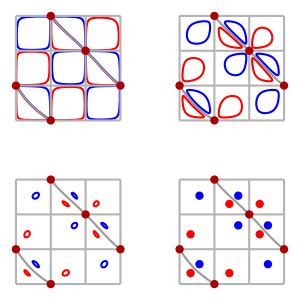

```mathematica
parallelplottab4=
GraphicsGrid[{{parallelplottab⟦1⟧,parallelplottab⟦16⟧},
                           {parallelplottab⟦48⟧,parallelplottab⟦52⟧}},
                               Spacings->{60,60},
                               Background->None,
                               ImageSize->300]
```